```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Reference Solution (N=40)

```mathematica
Clear[θRef]
```

```mathematica
θRef[x_] = 0.9884735156696915 x-1.1457678311582425*^-10 (Cosh[1.2078840101317283 x]-Sinh[1.2078840101317283 x])+1.1457678311728836*^-10 (Cosh[1.2078840101317283 x]+Sinh[1.2078840101317283 x])+6.933239237405841*^-10 (Cosh[1.3078453876891523 x]-Sinh[1.3078453876891523 x])-6.933239237401193*^-10 (Cosh[1.3078453876891523 x]+Sinh[1.3078453876891523 x])-2.1060693855761778*^-8 (Cosh[1.4201039622641722 x]-Sinh[1.4201039622641722 x])+2.1060693855765543*^-8 (Cosh[1.4201039622641722 x]+Sinh[1.4201039622641722 x])-2.6992029959027656*^-7 (Cosh[1.5481284098563823 x]-Sinh[1.5481284098563823 x])+2.699202995902824*^-7 (Cosh[1.5481284098563823 x]+Sinh[1.5481284098563823 x])-4.210084451095493*^-6 (Cosh[1.6964567741916035 x]-Sinh[1.6964567741916035 x])+4.210084451095377*^-6 (Cosh[1.6964567741916035 x]+Sinh[1.6964567741916035 x])-0.00003118740478035235 (Cosh[1.8716019970135933 x]-Sinh[1.8716019970135933 x])+0.000031187404780352396 (Cosh[1.8716019970135933 x]+Sinh[1.8716019970135933 x])-0.00014648630693050077 (Cosh[2.084723525254245 x]-Sinh[2.084723525254245 x])+0.00014648630693049947 (Cosh[2.084723525254245 x]+Sinh[2.084723525254245 x])-0.00039749988958803415 (Cosh[2.3577417474531877 x]-Sinh[2.3577417474531877 x])+0.0003974998895880341 (Cosh[2.3577417474531877 x]+Sinh[2.3577417474531877 x])-0.0007222957924572226 (Cosh[2.7318724706353126 x]-Sinh[2.7318724706353126 x])+0.0007222957924572248 (Cosh[2.7318724706353126 x]+Sinh[2.7318724706353126 x])-0.0009273335235258298 (Cosh[3.282073516752524 x]-Sinh[3.282073516752524 x])+0.0009273335235258277 (Cosh[3.282073516752524 x]+Sinh[3.282073516752524 x])-0.0009098029667887219 (Cosh[4.162412100887137 x]-Sinh[4.162412100887137 x])+0.0009098029667887222 (Cosh[4.162412100887137 x]+Sinh[4.162412100887137 x])-0.0005701566488494193 (Cosh[5.7687839178768066 x]-Sinh[5.7687839178768066 x])+0.0005701566488494196 (Cosh[5.7687839178768066 x]+Sinh[5.7687839178768066 x])-0.0001268351754459892 (Cosh[9.551054823962051 x]-Sinh[9.551054823962051 x])+0.0001268351754459892 (Cosh[9.551054823962051 x]+Sinh[9.551054823962051 x])-1.3502774955260917*^-8 (Cosh[28.55918996701305 x]-Sinh[28.55918996701305 x])+1.3502774955260907*^-8 (Cosh[28.55918996701305 x]+Sinh[28.55918996701305 x]);
```

## Solution Uniform

```mathematica
Do[resultUniform[ii]=GetSolution[ii,0.1,1,bcMBC[ii]];
errorUniform[ii]=Abs[NIntegrate[x(resultUniform[ii]⟦3⟧-θRef[x]),{x,-0.5,0.5}]],{ii,Range[6,12,2]}];
```

```mathematica
GetSolution[6,0.1,1,bcMBC[6]]
```

{-1.40717 x+0.00689098 (Cosh[4.47214 x]-Sinh[4.47214 x])-0.00689098 (Cosh[4.47214 x]+Sinh[4.47214 x]),0.,0.995021 x-0.00487266 (Cosh[4.47214 x]-Sinh[4.47214 x])+0.00487266 (Cosh[4.47214 x]+Sinh[4.47214 x]),-0.172343,0.00421985 (Cosh[4.47214 x]-Sinh[4.47214 x])-0.00421985 (Cosh[4.47214 x]+Sinh[4.47214 x]),0.00421985 (Cosh[4.47214 x]-Sinh[4.47214 x])+0.00421985 (Cosh[4.47214 x]+Sinh[4.47214 x])}

```mathematica
resultUniform[6]⟦3⟧
```

0.995021 x-0.00487266 (Cosh[4.47214 x]-Sinh[4.47214 x])+0.00487266 (Cosh[4.47214 x]+Sinh[4.47214 x])

```mathematica
errorUniform[12]
```

0.00032047

```mathematica
Range[6,12,2]
```

## Numerical Solution Adaptive

```mathematica
Clear[result]
```

```mathematica
Do[result[ii]=Import[StringJoin["../2x1v_moments_Inflow_Adp/M_6_8_10_12/result_cycle",ToString[ii],"_Kn_0p1.txt"],"Table"];
result[ii]=Interpolation[Transpose[{result[ii]⟦All,1⟧,result[ii]⟦All,5⟧}]];
error[ii]=Abs[NIntegrate[x(result[ii][x]-θRef[x-0.5]),{x,0,1}]];,{ii,0,3}];
```

```mathematica
Do[FeIndex[ii]=Import[StringJoin["../2x1v_moments_Inflow_Adp/M_6_8_10_12/fe_index_cycle",ToString[ii],"_Kn_0p1.txt"],"Table"];,{ii,0,3}];
```

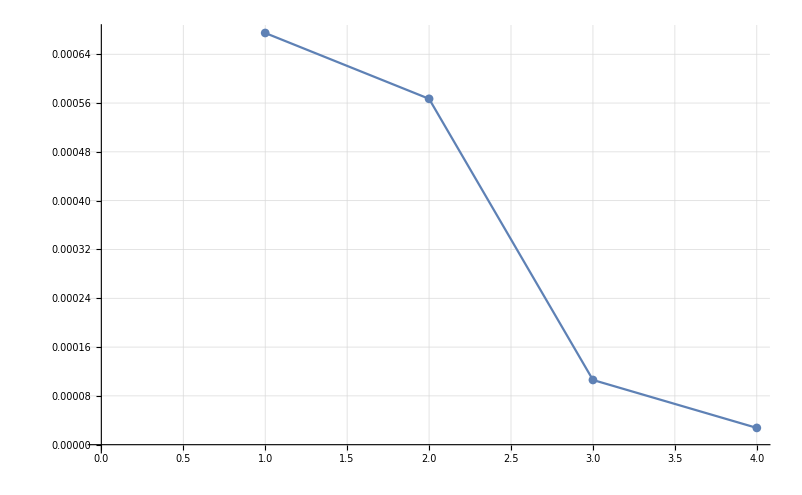

```mathematica
ListPlot[Table[error[ii],{ii,0,3}],GridLines->Automatic,Joined->True,PlotMarkers->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

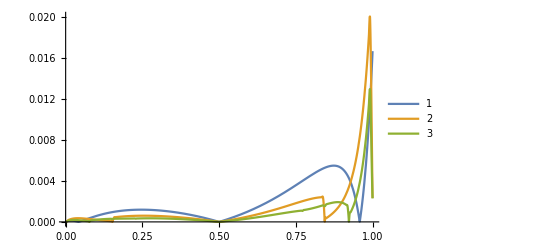

```mathematica
Plot[{Abs[x(result[0][x]-θRef[x-0.5])],Abs[x(result[1][x]-θRef[x-0.5])],Abs[x(result[2][x]-θRef[x-0.5])]},{x,0,1},PlotRange->Full,PlotLegends->{"1","2","3"}]
```

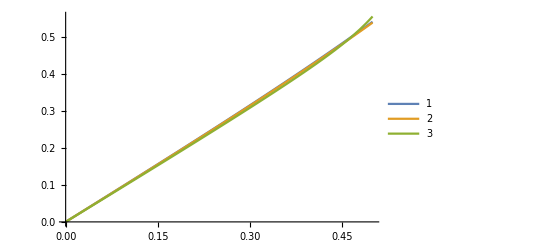

```mathematica
Plot[{resultUniform[6]⟦3⟧,result[0][x+0.5],result[0][x+0.5],θRef[x]},{x,0.0,0.5},PlotLegends->{"1","2","3"}]
```